# Projekt 2 - Fördelningar

## IX1501

## Uppgift 1: Distribution Parameters

Uppgift 1 består av tre deluppgifter:

Estimera μ och σ från delvis slumpad data.

Testa de tre följande modellerna till den slumpade datan, och välj ut den som bäst representerar den slumpade datan.

pdf(x)∝e^(-a x),x≥0

pdf(x)∝x e^(-a x),x≥0

pdf(x)∝x (x+b)e^(-a x),x≥0

Beräkna ett “Confidence Interval” på 95% för de valda konstanterna i den valda modellen. Intervallet får inte avvika mer än 10% från mellanvärdet, e.g. μ (1±0.05).

Den slumpade datan genereras från en fördefinierad fil vid namn “Projekt2.m”

## Estimera μ och σ

```mathematica
n=1000;
𝕩=randomNumber[0,n];
Short[𝕩]
```

{1.91606,12.8234,«997»,10.3068}

```mathematica
μ=Mean[𝕩]
σ=StandardDeviation[𝕩]
```

5.36906

3.39978

## Testa de tre modellerna

```mathematica
n=1000;
𝕩=randomNumber[0,n];
```

```mathematica
f1[x_]:=ⅇ^(-a*x);
f2[x_]:=x*ⅇ^(-a*x);
f3[x_]:=x*(x+b)*ⅇ^(-a*x);
```

```mathematica
i1=Integrate[f1[x],{x,0,∞},Assumptions->{a>0}];
i2=Integrate[f2[x],{x,0,∞},Assumptions->{a>0}];
i3=Integrate[f3[x],{x,0,∞},Assumptions->{{a>0},{b>0}}];
```

```mathematica
c1=1/i1;
c2=1/i2;
c3=1/i3;
```

```mathematica
pdf1[x_]:=c1*f1[x]
pdf2[x_]:=c2*f2[x]
pdf3[x_]:=c3*f3[x]
```

```mathematica
𝒟1[a_]:=ProbabilityDistribution[pdf1[x],{x,0,∞},Assumptions->{a>0}]
𝒟2[a_]:=ProbabilityDistribution[pdf2[x],{x,0,∞},Assumptions->{a>0}]
𝒟3[a_,b_]:=ProbabilityDistribution[pdf3[x],{x,0,∞},Assumptions->{{a>0},{b>0}}]
```

```mathematica
myDist1=EstimatedDistribution[𝕩,𝒟1[a]];
myDist2=EstimatedDistribution[𝕩,𝒟2[a]];
myDist3=EstimatedDistribution[𝕩,𝒟3[a,b]];
```

ProbabilityDistribution[0.190622 ⅇ^(-0.190622 x),{x,0,∞},Assumptions→{True}]

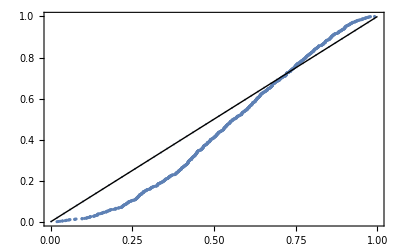

```mathematica
myDist1
ProbabilityPlot[𝕩,myDist1]
```

ProbabilityDistribution[0.145347 x ⅇ^(-0.381243 x),{x,0,∞},Assumptions→{True}]

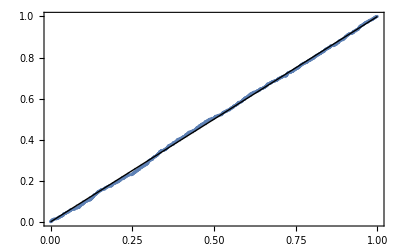

```mathematica
myDist2
ProbabilityPlot[𝕩,myDist2]
```

ProbabilityDistribution[0.0274209 x (4.32678+x) ⅇ^(-0.482083 x),{x,0,∞},Assumptions→{{True},{True}}]

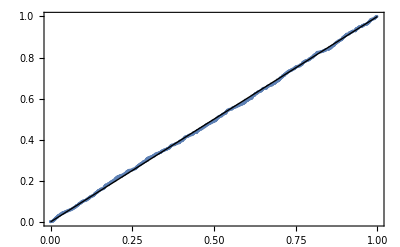

```mathematica
myDist3
ProbabilityPlot[𝕩,myDist3]
```

## Beräkna konfidensintervall

```mathematica
α=0.7173293780432751;
β=0.5393988397118393;
```

```mathematica
q=Quantile[myDist3,0.975];
```

```mathematica
s=StandardDeviation[𝕩];
```

```mathematica
n = 1000;
```

```mathematica
ciα = {α - q*(s/Sqrt[n]), α + q*(s/Sqrt[n])}
ciβ = {β- q*(s/Sqrt[n]), β + q*(s/Sqrt[n])}
```

{-0.957431,2.39209}

{-1.13536,2.21416}

```mathematica
Clear[α,β]
```

```mathematica
cilenα=ciα⟦2⟧-ciα⟦1⟧
cilenβ=ciβ⟦2⟧-ciβ⟦1⟧
```

3.34952

3.34952

```mathematica
margin=2;
nnew=Ceiling[margin*n*(cilenα/ 0.1)^2]
```

1725603

```mathematica
𝕩=randomNumber[0,nnew];
```

```mathematica
EstimatedDistribution[𝕩,𝒟3[a,b]]
```

ProbabilityDistribution[0.0355465 x (3.02533+x) ⅇ^(-0.499787 x),{x,0,∞},Assumptions→{{True},{True}}]

```mathematica
α=0.4997866602912788;
β=3.02533003422653;
```

```mathematica
s=StandardDeviation[𝕩]
```

3.35997

```mathematica
ciα = {α - q*(s/Sqrt[nnew]), α + q*(s/Sqrt[nnew])}
ciα = {β - q*(s/Sqrt[nnew]), β + q*(s/Sqrt[nnew])}
```

{0.464813,0.53476}

{2.99036,3.0603}

## Uppgift 2: Which Distribution?

I uppgift 2 ska vi använda fördelningarna i = 1,2,..., 6 i randomNumber funktionen och svara på dessa frågor:

Använd räta linjens metod för att bestäma en distributionsmodell för var och en av data-varianterna.

Estimera parametrarna för de olika distributionsmodellerna

Beräkna 95% konfidensintervaller för parametrarna. Intervallet bör inte vara längre än 10% av dess medelvärde.

## Bestäm fördelningsmodell

```mathematica
dist1[i_,n_, a_, plotName_, color_] := 
Module[{𝕩, 𝒩, plot, μ, σ},
𝕩=randomNumber[i,n];
𝒩=EstimatedDistribution[𝕩,a];

plot =ProbabilityPlot[𝕩,𝒩, PlotLegends->LineLegend[{color},{plotName}], PlotStyle->color];
{𝕩, plot}
]
```

```mathematica
n = 1000;
```

```mathematica
normalD = NormalDistribution[a,b];
gammaD = GammaDistribution[a,b];
expD = ExponentialDistribution[a];
weibullD = WeibullDistribution[a,b]; 
geoD = GeometricDistribution[a];
poissonD = PoissonDistribution[a];
binD = BinomialDistribution[a,b];
```

```mathematica
(*Distribution 1*)
```

```mathematica
{𝕩11, plot11} = dist1[1,n,normalD,"NormalDistribution", Blue ];
{𝕩12, plot12} = dist1[1,n, gammaD, "GammaDistribution", Red];
{𝕩13, plot13} = dist1[1,n, expD,"ExponentialDistribution", Green ];
{𝕩14, plot14} = dist1[1,n, weibullD,"WeibullDistribution", Black ];
```

```mathematica
(*Distribution 2*)
```

```mathematica
{𝕩21, plot21} = dist1[2,n, normalD,"NormalDistribution", Blue ];
{𝕩22, plot22} = dist1[2,n, poissonD, "PoissonDistribution", Red];
{𝕩23, plot23} = dist1[2,n, expD,"ExponentialDistribution", Green ];
{𝕩24, plot24} = dist1[2,n,geoD,"GeometricDistribution", Black ];
```

```mathematica
(*Distribution 3*)
```

```mathematica
{𝕩31, plot31} = dist1[3,n,normalD,"NormalDistribution", Blue ];
{𝕩32, plot32} = dist1[3,n, gammaD, "GammaDistribution", Red];
{𝕩33, plot33} = dist1[3,n, expD,"ExponentialDistribution", Green ];
{𝕩34, plot34} = dist1[3,n, weibullD,"WeibullDistribution", Black ];
```

```mathematica
(*Distribution 4*)
```

```mathematica
{𝕩41, plot41} = dist1[4,n,normalD,"NormalDistribution", Blue ];
```

```mathematica
(*Distribution 5*)
```

```mathematica
{𝕩51, plot51} = dist1[5,n,normalD,"NormalDistribution", Blue ];
{𝕩52, plot52} = dist1[5,n,expD,"ExponentialDistribution", Red ];
{𝕩53, plot53} = dist1[5,n,geoD,"GeometricDistribution", Green ];
{𝕩54, plot54} = dist1[5,n,poissonD,"PoissonDistribution", Yellow ];
{𝕩55, plot55} = dist1[5,n,binD,"BinomialDistribution", Brown ];
```

```mathematica
(*Distribution 6*)
```

```mathematica
{𝕩61, plot61} = dist1[6,n,normalD,"NormalDistribution", Blue ];
{𝕩62, plot62} = dist1[6,n,expD,"ExponentialDistribution", Red ];
{𝕩63, plot63} = dist1[6,n,geoD,"GeometricDistribution", Green ];
{𝕩64, plot64} = dist1[6,n,poissonD,"PoissonDistribution", Yellow ];
{𝕩65, plot65} = dist1[6,n,gammaD,"GammaDistribution", Brown ];
```

```mathematica
(*GammaDistribution for Distribution 1*)
```

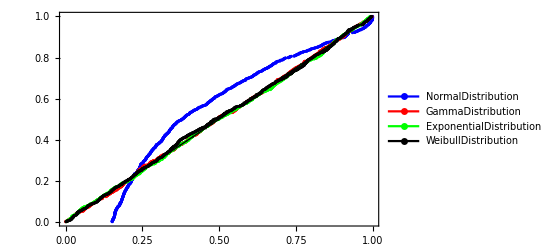

```mathematica
Show[plot11,plot12, plot13, plot14]
```

```mathematica
(*GeometricDistribution for Distribution 2*)
```

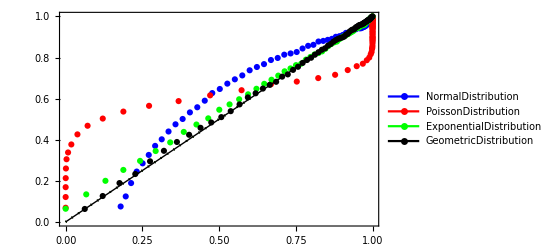

```mathematica
Show[plot21,plot22, plot23, plot24]
```

```mathematica
(*GammaDistribution for Distribution 3*)
```

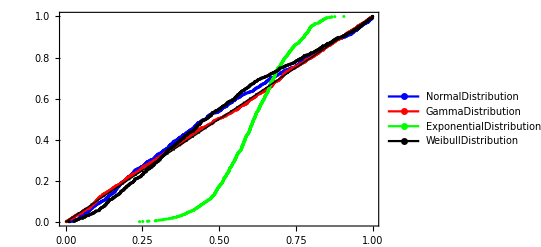

```mathematica
Show[plot31,plot32, plot33, plot34]
```

```mathematica
(*NormalDistribution for Distribution 4*)
```

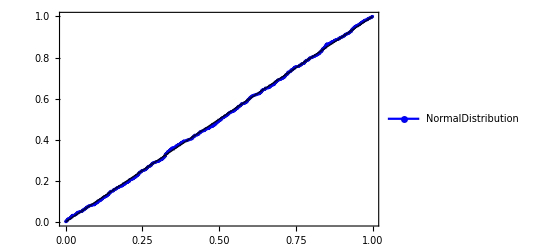

```mathematica
plot41
```

```mathematica
(*BinomialDistribution for Distribution 5*)
```

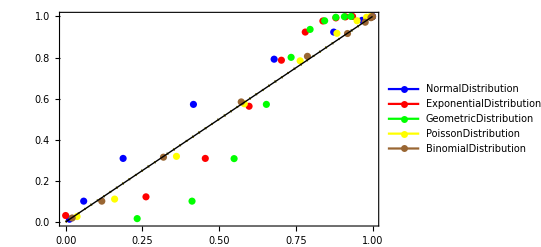

```mathematica
Show[plot51,plot52, plot53, plot54, plot55]
```

```mathematica
(*PoissonDistribution for Distribution 6*)
```

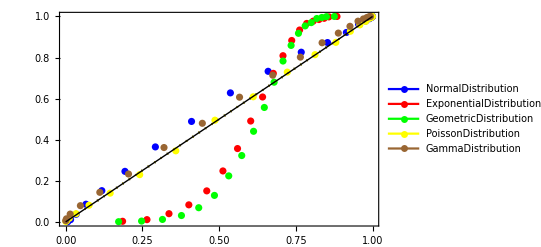

```mathematica
Show[plot61,plot62, plot63, plot64, plot65]
```

## Estimera parametrarna

```mathematica
(*Distribution 1*)
```

```mathematica
EstimatedDistribution[𝕩12,gammaD]
```

GammaDistribution[0.970294,0.216259]

```mathematica
(*Distribution 2*)
```

```mathematica
EstimatedDistribution[𝕩24,geoD]
```

GeometricDistribution[0.0690512]

```mathematica
(*Distribution 3*)
```

```mathematica
EstimatedDistribution[𝕩32,gammaD]
```

GammaDistribution[7.96105,1.61395]

```mathematica
(*Distribution 4*)
```

```mathematica
EstimatedDistribution[𝕩41,normalD]
```

NormalDistribution[2.98273,5.15498]

```mathematica
(*Distribution 5*)
```

```mathematica
EstimatedDistribution[𝕩54,poissonD]
```

PoissonDistribution[3.275]

```mathematica
(*Distribution 6*)
```

```mathematica
EstimatedDistribution[𝕩64,poissonD]
```

PoissonDistribution[9.758]

## Beräkna konfidensintervaller

En metod som tar ut konfidensintervall för α som inte är längre än 10% av dess medelvärde

```mathematica
cltαβ[d_, m_,a_] := 
Module[{i=1 , j=1,n=2,𝕩, 𝕒,𝕓, findαβ, ciα1, ciα2, ciβ1, ciβ2, m𝕒,m𝕓},
findαβ[data_]:=List@@EstimatedDistribution[data,a];
While[i==1 || j == 1,
𝕩=randomNumber[d,{n,m}];
{𝕒,𝕓} = Transpose[findαβ/@𝕩];
m𝕒 = Mean[𝕒];
m𝕓 = Mean[𝕓];
If[i ≠ 0,
{ciα1, ciα2}=MeanCI[𝕒, ConfidenceLevel->0.95];
 0];
If[j≠ 0,
{ciβ1, ciβ2}=MeanCI[𝕓, ConfidenceLevel->0.95];
0];
Which[ciα1 ≥m𝕒*0.95 && m𝕒 * 1.05 ≥ ciα1, i=0]; 
Which[ciβ1 ≥ m𝕓 *0.95&& m𝕓 *1.05 ≥ ciβ2,  j=0]; 
n++;];
{{ciα1, ciα2}, {ciβ1, ciβ2} }
]
```

En metod som tar ut konfidensintervall för α och β som inte är längre än 10% av dess medelvärde

```mathematica
cltα[d_, m_,a_] := 
Module[{i=1 ,n=2,𝕩, 𝕒, findα, ciα1, ciα2, m𝕒},
findα[data_]:=List@@EstimatedDistribution[data,a];
While[i==1 ,
𝕩=randomNumber[d,{n,m}];
{𝕒} = Transpose[findα/@𝕩];
m𝕒 = Mean[𝕒];
{ciα1, ciα2}=MeanCI[𝕒, ConfidenceLevel->0.95];
Which[ciα1 ≥m𝕒*0.95 && m𝕒 * 1.05 ≥ ciα1, i=0]; 
n++;];
{ciα1, ciα2}
]
```

```mathematica
cltαβ[1, n, gammaD]
```

{{0.964902,1.01956},{0.213129,0.231411}}

```mathematica
cltα[2, n, geoD ]
```

{0.0631177,0.0654572}

```mathematica
cltαβ[3, n, gammaD]
```

{{7.76802,8.49892},{1.52164,1.61731}}

```mathematica
cltαβ[4, n, normalD]
```

{{2.96675,3.15467},{4.9226,5.26378}}

```mathematica
cltαβ[5, n,binD]
```

{{10.9128,11.9205},{0.277445,0.303625}}

```mathematica
cltα[5, n,poissonD]
```

{3.14326,3.29407}

```mathematica
cltα[6, n, poissonD]
```

{9.54735,10.0513}